```mathematica
m12[t_]:={{Cos[t],-Sin[t],0},{Sin[t],Cos[t],0},{0,0,1}}
```

```mathematica
m12[t1]//MatrixForm
```

(Cos[t1] | -Sin[t1] | 0
Sin[t1] | Cos[t1] | 0
0 | 0 | 1)

```mathematica
m23[t_]:={{1,0,0},{0,Cos[t],-Sin[t]},{0,Sin[t],Cos[t]}}
```

```mathematica
m23[t2]//MatrixForm
```

(1 | 0 | 0
0 | Cos[t2] | -Sin[t2]
0 | Sin[t2] | Cos[t2])

```mathematica
m31[t_]:={{Cos[t],0,Sin[t]},{0,1,0},{-Sin[t],0,Cos[t]}}
```

```mathematica
m31[t3]//MatrixForm
```

(Cos[t3] | 0 | Sin[t3]
0 | 1 | 0
-Sin[t3] | 0 | Cos[t3])

```mathematica
mm[t1_,t2_,t3_]:=m12[t1].m23[t2].m31[t3]
```

```mathematica
mm[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
m=2;Plot3D[1/MaxSum[mm[t1,0,t3+Pi/2]],{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->50,MaxRecursion->4]
```

-Graphics3D-

```mathematica
m=2;Plot3D[{RowSums[mm[t1,0,t3+Pi/2]][[1]],RowSums[mm[t1,0,t3+Pi/2]][[2]],RowSums[mm[t1,0,t3+Pi/2]][[3]]},{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->50,MaxRecursion->4,PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

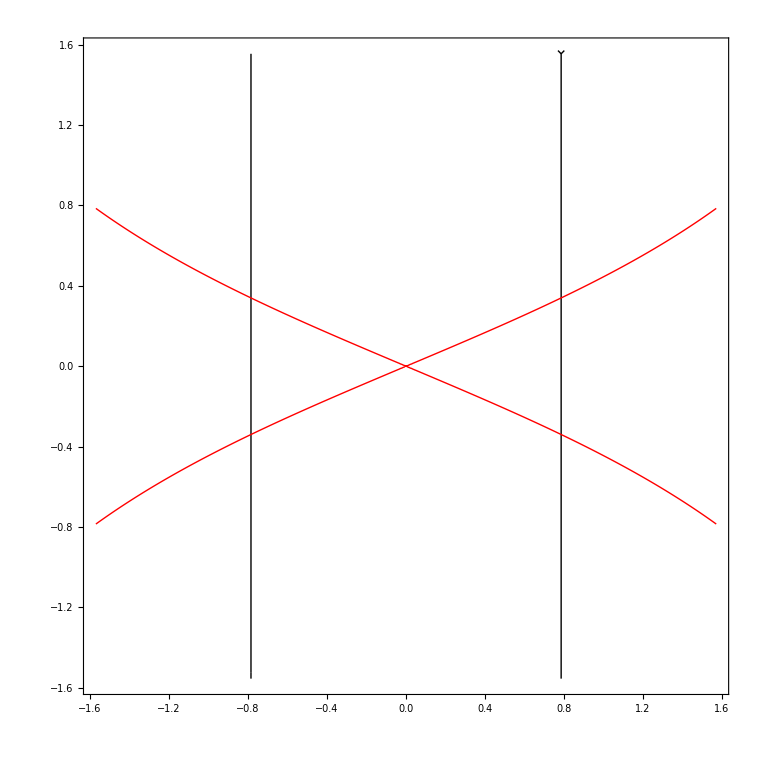

```mathematica
m=2;ContourPlot[{RowSums[mm[t1,0,t3+Pi/2]][[1]]-RowSums[mm[t1,0,t3+Pi/2]][[2]],RowSums[mm[t1,0,t3+Pi/2]][[2]]-RowSums[mm[t1,0,t3+Pi/2]][[3]]},{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->50,MaxRecursion->4,Contours->{0},ContourStyle->{{Black,Thick},{Red,Thick}},ContourShading->None]
```

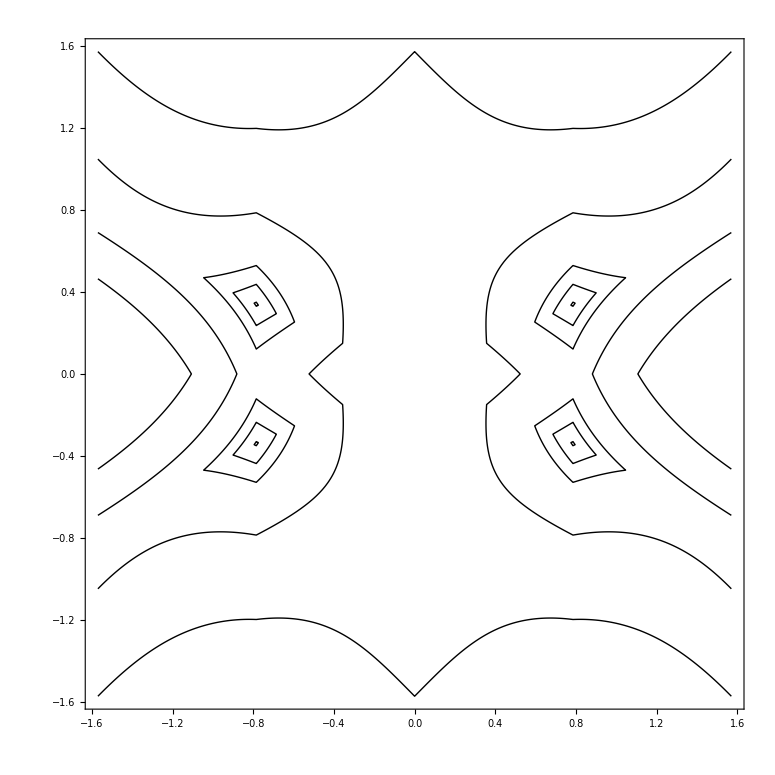

```mathematica
m=2;ContourPlot[Abs[RowSums[mm[t1,0,t3+Pi/2]][[1]]-RowSums[mm[t1,0,t3+Pi/2]][[2]]]+Abs[RowSums[mm[t1,0,t3+Pi/2]][[2]]-RowSums[mm[t1,0,t3+Pi/2]][[3]]],{t1,-Pi/2,Pi/2},{t3,-Pi/2,Pi/2},Exclusions->False,PlotPoints->50,MaxRecursion->4,Contours->{2,1,0.5,0.2,0.1,0.01},ContourStyle->{{Black,Thick}},ContourShading->None]
```

```mathematica
mm[t1,t2,t3]//MatrixForm
```

(Cos[t1] Cos[t3]-Sin[t1] Sin[t2] Sin[t3] | -Cos[t2] Sin[t1] | Cos[t3] Sin[t1] Sin[t2]+Cos[t1] Sin[t3]
Cos[t3] Sin[t1]+Cos[t1] Sin[t2] Sin[t3] | Cos[t1] Cos[t2] | -Cos[t1] Cos[t3] Sin[t2]+Sin[t1] Sin[t3]
-Cos[t2] Sin[t3] | Sin[t2] | Cos[t2] Cos[t3])

```mathematica
mm[Pi/4,0,1.2309594173407077]//MatrixForm
```

(0.235702 | -0.707107 | 0.666667
0.235702 | 0.707107 | 0.666667
-0.942809 | 0. | 0.333333)

```mathematica
RowSums[mm[Pi/4,0,1.2309594173407077]]
```

{0.942809,0.942809,0.942809}